```mathematica
(*Continuando ejercicios del libro - Objetos Graficos*)
```

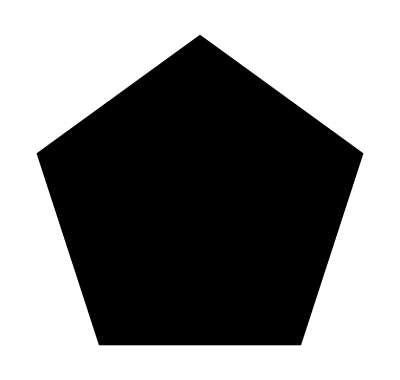
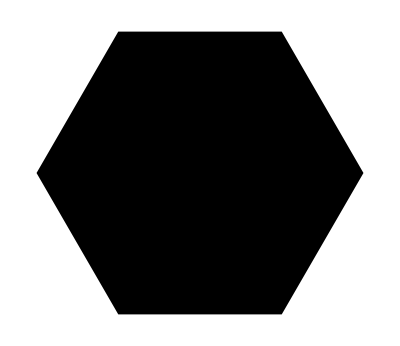
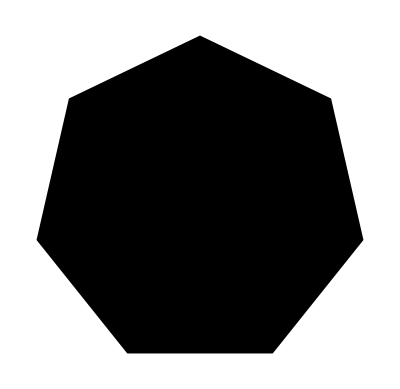
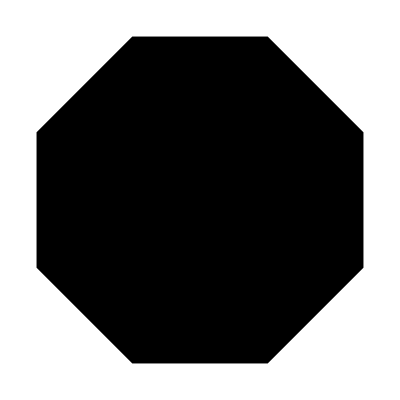
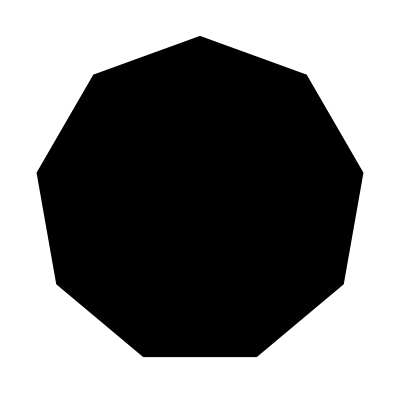
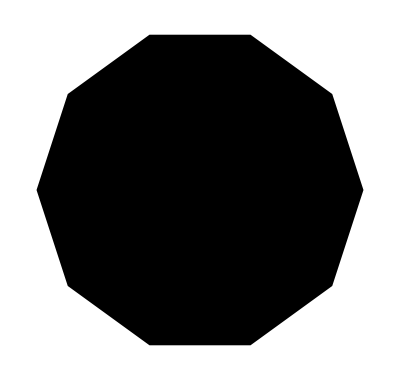

```mathematica
Table[Graphics[RegularPolygon[n]],{n,5,10}]
```

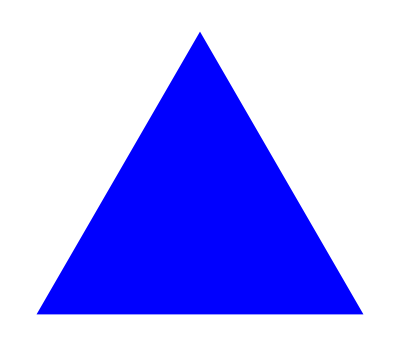

```mathematica
Graphics[Style[RegularPolygon[3],Blue]]
```

```mathematica
{Graphics3D[Cone[]],Graphics3D@Cylinder[]}
```

{-Graphics3D-,-Graphics3D-}


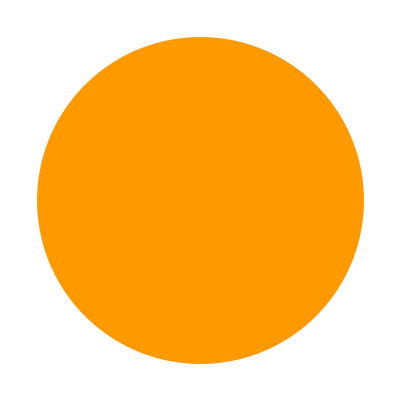
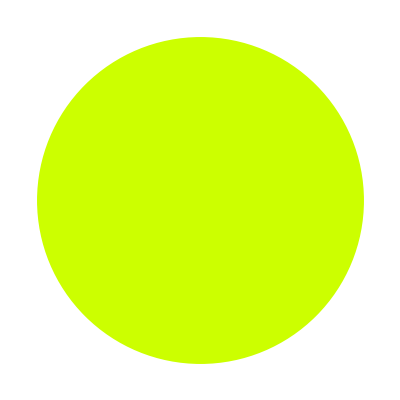
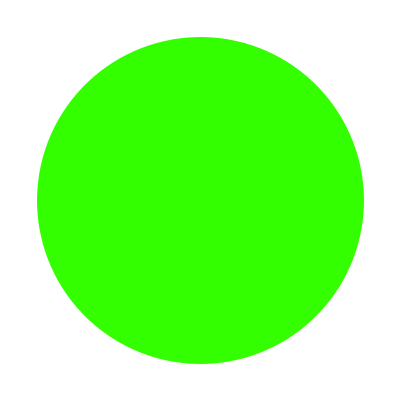
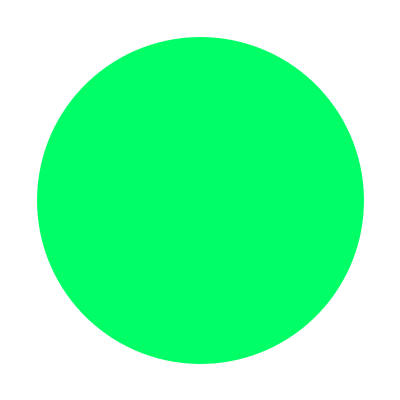
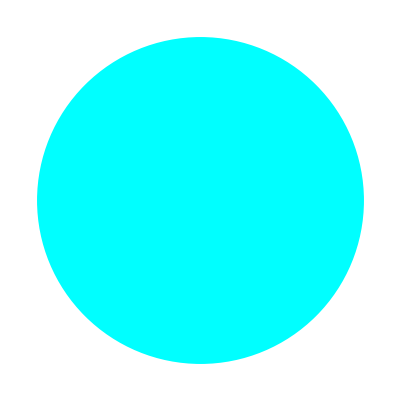
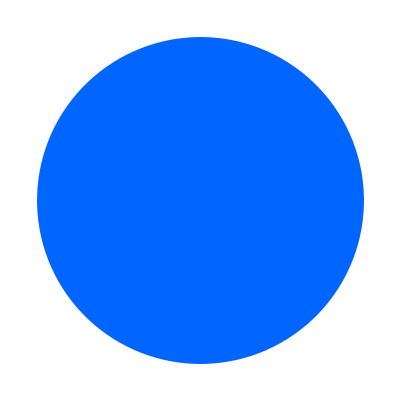
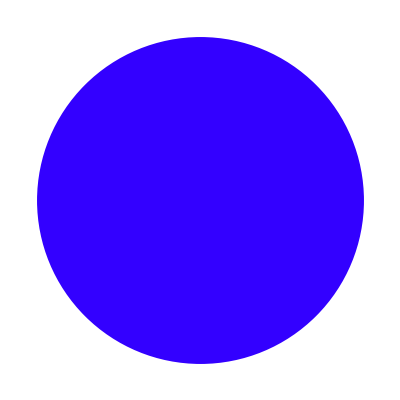
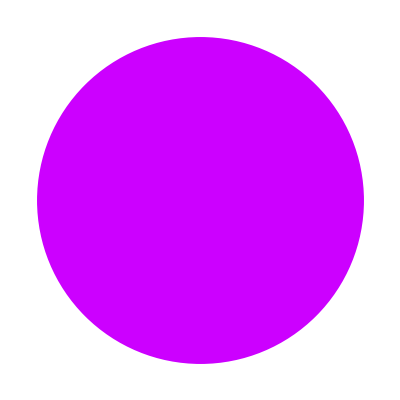
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Lista con elementos que sean discos con tonalidades de 0 a 1 en steps de 0.1*)
Table[Graphics[Style[Disk[],Hue[c]]],{c,0,1.,0.1}]
```

```mathematica
(*Obtener coordenadas aleatorias*)
RandomInteger[20,{10,3}] (*10 puntos con 3 coordenadas, que van del 0 al 20*)
```

{{9,5,10},{8,9,19},{8,12,2},{18,16,1},{12,14,16},{2,8,12},{9,5,9},{4,17,20},{19,0,14},{7,14,0}}

```mathematica
(*Ejercicio ParaOlympics*)

(*Veamos si Table se puede hacer con listas*)
e={3,4,5}
Table[e[[n]],{n,1,2}]
```

{3,4,5}

{3,4}

```mathematica
lis={{0,Blue},{2.2,Black},{4.4,Red}}
```

{{0,RGBColor[0, 0, 1]},{2.2,GrayLevel[0]},{4.4,RGBColor[1, 0, 0]}}

```mathematica
lis[[1]][[2]] (*El segundo elemento del primer elemento de la lista lis*)
```

RGBColor[1, 0, 0]

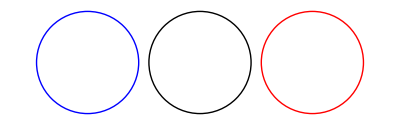

```mathematica
(*Para aplicarlo a los circulos*)
uppr=Graphics@Table[Style[Circle[{lis[[i]][[1]],1}],lis[[i]][[2]]],{i,3}]
```

```mathematica
lisa={{1.1,Yellow},{3.3,Green}}
```

{{1.1,RGBColor[1, 1, 0]},{3.3,RGBColor[0, 1, 0]}}

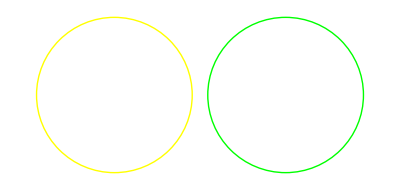

```mathematica
lwr=Graphics@Table[Style[Circle[{lisa[[i]][[1]],0},1],lisa[[i]][[2]]],{i,2}]
```

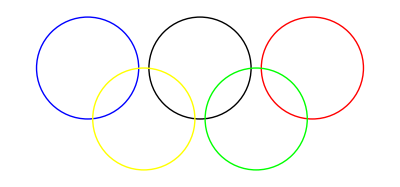

```mathematica
Show[uppr,lwr]
```